#### Conway’s game of life: A simple model

Set the notebook’s language to English and the notebook directory.

```mathematica
CurrentValue[EvaluationNotebook[],DefaultNaturalLanguage]="English";
SetDirectory[NotebookDirectory[]];
```

Update equation for Conway’s game of life from one density to the density of the next time step.

```mathematica
updateFunc[p_]:=Binomial[8, 2] * p^3 *(1 - p)^6 + Binomial[8,3] * p^3 * (1 - p)^5
```

In the  equilibrium the density doesn’t change and is thus given by the equation below.

```mathematica
Solve[ρ == updateFunc[ρ]&& 0≤ ρ ≤1, ρ]//N
```

{{ρ→0.},{ρ→0.192469},{ρ→0.370174}}

Check which initial densities result in which final densities.

```mathematica
numberOfRecursions = 20;
initialDensities = Range[0.,1.,0.005];
densityEvolution=Map[RecurrenceTable[{ρ[n+1]==updateFunc[ρ[n]],ρ[1]==#},ρ,{n,1,numberOfRecursions}]&,initialDensities];
finalDenisities=Map[#[[-1]]&,densityEvolution];
```

Plotting the initial densities and final densities against each other. Also plots the time evolution of the density for different starting values

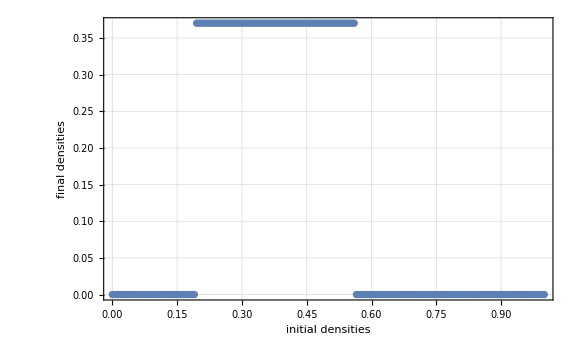
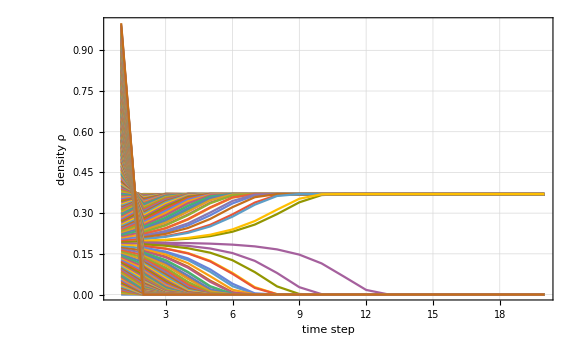

```mathematica
initialVsFinalDensity=Partition[Riffle[initialDensities,finalDenisities],2];
Row[{ListPlot[initialVsFinalDensity, Frame->True, GridLines->Automatic, ImageSize->Large,FrameLabel->{"initial densities", "final densities"}, LabelStyle->Directive[FontSize->18, FontFamily->"Latin Modern Math",Black]],
ListPlot[densityEvolution, Frame->True, GridLines->Automatic, ImageSize->Large,FrameLabel->{"time step", "density ρ"}, LabelStyle->Directive[FontSize->18, FontFamily->"Latin Modern Math",Black],PlotRange->All,Joined->True]}]
```

Plotting the data given by the C++ simulation.

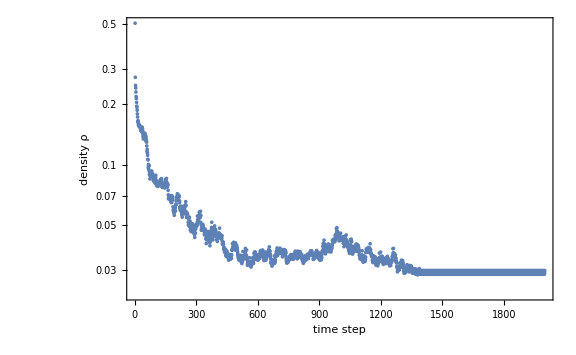

```mathematica
simulatedDensity=Drop[Import["data.csv","List"],1];
ListLogPlot[simulatedDensity,PlotRange->All, ImageSize->Large ,GridLines->Automatic, Frame->True,FrameLabel->{"time step","density ρ"},LabelStyle->Directive[FontSize->18, FontFamily->"Latin Modern Math",Black]]
```